# Omicron analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-countries

```mathematica
dataset="omicron-countries";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01","2022-03-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

### Countries

```mathematica
countriesToDrop={"Philippines"};
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-10-15

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2022-01-30

```mathematica
countries=Union[seqData[[All,2]]]
```

{Australia,Austria,Brazil,Canada,Chile,Colombia,Croatia,Denmark,France,Germany,India,Ireland,Israel,Japan,Lithuania,Netherlands,New Zealand,Norway,Philippines,Singapore,Slovakia,South Africa,South Korea,Spain,Sweden,Switzerland,Thailand,United Kingdom,USA}

```mathematica
countries=Complement[countries,countriesToDrop]
```

{Australia,Austria,Brazil,Canada,Chile,Colombia,Croatia,Denmark,France,Germany,India,Ireland,Israel,Japan,Lithuania,Netherlands,New Zealand,Norway,Singapore,Slovakia,South Africa,South Korea,Spain,Sweden,Switzerland,Thailand,United Kingdom,USA}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countryVariantCounts[country_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==country&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
countrySequenceCounts[country_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==country][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->countrySequenceCounts[#][[-15;;-1]]&,countries]
```

{Australia→{{2022-01-16,139},{2022-01-17,180},{2022-01-18,193},{2022-01-19,145},{2022-01-20,122},{2022-01-21,102},{2022-01-22,70},{2022-01-23,63},{2022-01-24,75},{2022-01-25,30},{2022-01-26,33},{2022-01-27,46},{2022-01-28,46},{2022-01-29,36},{2022-01-30,31}},Austria→{{2022-01-16,87},{2022-01-17,53},{2022-01-18,36},{2022-01-19,53},{2022-01-20,81},{2022-01-21,71},{2022-01-22,130},{2022-01-23,89},{2022-01-24,85},{2022-01-25,135},{2022-01-26,11},{2022-01-27,22},{2022-01-28,22},{2022-01-29,0},{2022-01-30,0}},Brazil→{{2022-01-16,42},{2022-01-17,96},{2022-01-18,128},{2022-01-19,90},{2022-01-20,52},{2022-01-21,50},{2022-01-22,41},{2022-01-23,10},{2022-01-24,60},{2022-01-25,39},{2022-01-26,10},{2022-01-27,0},{2022-01-28,281},{2022-01-29,0},{2022-01-30,0}},Canada→{{2022-01-16,113},{2022-01-17,106},{2022-01-18,144},{2022-01-19,81},{2022-01-20,48},{2022-01-21,104},{2022-01-22,33},{2022-01-23,12},{2022-01-24,17},{2022-01-25,15},{2022-01-26,72},{2022-01-27,22},{2022-01-28,7},{2022-01-29,0},{2022-01-30,0}},Chile→{{2022-01-16,9},{2022-01-17,20},{2022-01-18,10},{2022-01-19,18},{2022-01-20,6},{2022-01-21,0},{2022-01-22,0},{2022-01-23,0},{2022-01-24,0},{2022-01-25,0},{2022-01-26,0},{2022-01-27,0},{2022-01-28,0},{2022-01-29,0},{2022-01-30,0}},Colombia→{{2022-01-16,31},{2022-01-17,22},{2022-01-18,1},{2022-01-19,1},{2022-01-20,1},{2022-01-21,5},{2022-01-22,0},{2022-01-23,9},{2022-01-24,8},{2022-01-25,4},{2022-01-26,2},{2022-01-27,0},{2022-01-28,0},{2022-01-29,0},{2022-01-30,0}},Croatia→{{2022-01-16,36},{2022-01-17,211},{2022-01-18,131},{2022-01-19,28},{2022-01-20,21},{2022-01-21,35},{2022-01-22,0},{2022-01-23,0},{2022-01-24,0},{2022-01-25,0},{2022-01-26,0},{2022-01-27,0},{2022-01-28,0},{2022-01-29,0},{2022-01-30,0}},Denmark→{{2022-01-16,1393},{2022-01-17,2042},{2022-01-18,2271},{2022-01-19,1947},{2022-01-20,1879},{2022-01-21,2390},{2022-01-22,1905},{2022-01-23,1944},{2022-01-24,2147},{2022-01-25,2262},{2022-01-26,1431},{2022-01-27,1500},{2022-01-28,644},{2022-01-29,485},{2022-01-30,283}},France→{{2022-01-16,206},{2022-01-17,2381},{2022-01-18,332},{2022-01-19,299},{2022-01-20,223},{2022-01-21,217},{2022-01-22,166},{2022-01-23,203},{2022-01-24,704},{2022-01-25,215},{2022-01-26,82},{2022-01-27,38},{2022-01-28,26},{2022-01-29,0},{2022-01-30,0}},Germany→{{2022-01-16,372},{2022-01-17,1891},{2022-01-18,2232},{2022-01-19,1530},{2022-01-20,1777},{2022-01-21,750},{2022-01-22,304},{2022-01-23,38},{2022-01-24,279},{2022-01-25,148},{2022-01-26,22},{2022-01-27,20},{2022-01-28,15},{2022-01-29,7},{2022-01-30,0}},India→{{2022-01-16,105},{2022-01-17,127},{2022-01-18,122},{2022-01-19,113},{2022-01-20,74},{2022-01-21,39},{2022-01-22,40},{2022-01-23,19},{2022-01-24,77},{2022-01-25,27},{2022-01-26,35},{2022-01-27,42},{2022-01-28,40},{2022-01-29,0},{2022-01-30,0}},Ireland→{{2022-01-16,25},{2022-01-17,39},{2022-01-18,23},{2022-01-19,27},{2022-01-20,14},{2022-01-21,14},{2022-01-22,29},{2022-01-23,28},{2022-01-24,30},{2022-01-25,0},{2022-01-26,0},{2022-01-27,0},{2022-01-28,0},{2022-01-29,0},{2022-01-30,0}},Israel→{{2022-01-16,203},{2022-01-17,153},{2022-01-18,175},{2022-01-19,96},{2022-01-20,371},{2022-01-21,401},{2022-01-22,284},{2022-01-23,209},{2022-01-24,475},{2022-01-25,559},{2022-01-26,217},{2022-01-27,2},{2022-01-28,0},{2022-01-29,0},{2022-01-30,0}},Japan→{{2022-01-16,12},{2022-01-17,590},{2022-01-18,21},{2022-01-19,23},{2022-01-20,11},{2022-01-21,24},{2022-01-22,9},{2022-01-23,2},{2022-01-24,10},{2022-01-25,3},{2022-01-26,2},{2022-01-27,17},{2022-01-28,1},{2022-01-29,0},{2022-01-30,0}},Lithuania→{{2022-01-16,18},{2022-01-17,27},{2022-01-18,30},{2022-01-19,17},{2022-01-20,7},{2022-01-21,9},{2022-01-22,5},{2022-01-23,0},{2022-01-24,0},{2022-01-25,0},{2022-01-26,0},{2022-01-27,0},{2022-01-28,0},{2022-01-29,0},{2022-01-30,0}},Netherlands→{{2022-01-16,229},{2022-01-17,258},{2022-01-18,249},{2022-01-19,248},{2022-01-20,160},{2022-01-21,141},{2022-01-22,177},{2022-01-23,142},{2022-01-24,91},{2022-01-25,41},{2022-01-26,35},{2022-01-27,35},{2022-01-28,39},{2022-01-29,0},{2022-01-30,0}},New Zealand→{{2022-01-16,39},{2022-01-17,67},{2022-01-18,23},{2022-01-19,24},{2022-01-20,16},{2022-01-21,18},{2022-01-22,22},{2022-01-23,38},{2022-01-24,33},{2022-01-25,12},{2022-01-26,16},{2022-01-27,22},{2022-01-28,20},{2022-01-29,0},{2022-01-30,0}},Norway→{{2022-01-16,61},{2022-01-17,32},{2022-01-18,27},{2022-01-19,15},{2022-01-20,13},{2022-01-21,6},{2022-01-22,8},{2022-01-23,54},{2022-01-24,18},{2022-01-25,69},{2022-01-26,10},{2022-01-27,10},{2022-01-28,8},{2022-01-29,0},{2022-01-30,0}},Singapore→{{2022-01-16,55},{2022-01-17,19},{2022-01-18,45},{2022-01-19,40},{2022-01-20,51},{2022-01-21,56},{2022-01-22,42},{2022-01-23,31},{2022-01-24,41},{2022-01-25,29},{2022-01-26,16},{2022-01-27,23},{2022-01-28,22},{2022-01-29,0},{2022-01-30,0}},Slovakia→{{2022-01-16,10},{2022-01-17,47},{2022-01-18,30},{2022-01-19,65},{2022-01-20,16},{2022-01-21,14},{2022-01-22,4},{2022-01-23,6},{2022-01-24,14},{2022-01-25,7},{2022-01-26,97},{2022-01-27,6},{2022-01-28,0},{2022-01-29,0},{2022-01-30,0}},South Africa→{{2022-01-16,12},{2022-01-17,43},{2022-01-18,23},{2022-01-19,5},{2022-01-20,3},{2022-01-21,1},{2022-01-22,1},{2022-01-23,2},{2022-01-24,25},{2022-01-25,1},{2022-01-26,0},{2022-01-27,0},{2022-01-28,0},{2022-01-29,0},{2022-01-30,0}},South Korea→{{2022-01-16,0},{2022-01-17,0},{2022-01-18,0},{2022-01-19,0},{2022-01-20,0},{2022-01-21,0},{2022-01-22,0},{2022-01-23,0},{2022-01-24,0},{2022-01-25,0},{2022-01-26,0},{2022-01-27,0},{2022-01-28,0},{2022-01-29,0},{2022-01-30,0}},Spain→{{2022-01-16,162},{2022-01-17,216},{2022-01-18,238},{2022-01-19,192},{2022-01-20,141},{2022-01-21,166},{2022-01-22,51},{2022-01-23,106},{2022-01-24,208},{2022-01-25,125},{2022-01-26,124},{2022-01-27,56},{2022-01-28,84},{2022-01-29,0},{2022-01-30,0}},Sweden→{{2022-01-16,122},{2022-01-17,277},{2022-01-18,242},{2022-01-19,48},{2022-01-20,287},{2022-01-21,62},{2022-01-22,26},{2022-01-23,90},{2022-01-24,182},{2022-01-25,137},{2022-01-26,97},{2022-01-27,74},{2022-01-28,42},{2022-01-29,0},{2022-01-30,0}},Switzerland→{{2022-01-16,205},{2022-01-17,470},{2022-01-18,265},{2022-01-19,225},{2022-01-20,152},{2022-01-21,83},{2022-01-22,133},{2022-01-23,103},{2022-01-24,368},{2022-01-25,271},{2022-01-26,123},{2022-01-27,36},{2022-01-28,24},{2022-01-29,0},{2022-01-30,0}},Thailand→{{2022-01-16,4},{2022-01-17,19},{2022-01-18,33},{2022-01-19,30},{2022-01-20,14},{2022-01-21,67},{2022-01-22,0},{2022-01-23,0},{2022-01-24,24},{2022-01-25,12},{2022-01-26,11},{2022-01-27,0},{2022-01-28,0},{2022-01-29,0},{2022-01-30,0}},United Kingdom→{{2022-01-16,6293},{2022-01-17,9905},{2022-01-18,8950},{2022-01-19,8086},{2022-01-20,7398},{2022-01-21,9673},{2022-01-22,6391},{2022-01-23,6106},{2022-01-24,8675},{2022-01-25,7325},{2022-01-26,7109},{2022-01-27,5310},{2022-01-28,5497},{2022-01-29,5499},{2022-01-30,4968}},USA→{{2022-01-16,4592},{2022-01-17,6715},{2022-01-18,10263},{2022-01-19,8568},{2022-01-20,4808},{2022-01-21,3402},{2022-01-22,3065},{2022-01-23,2208},{2022-01-24,4273},{2022-01-25,3322},{2022-01-26,1993},{2022-01-27,1198},{2022-01-28,591},{2022-01-29,0},{2022-01-30,0}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[country_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==country,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=15;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.00001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{logitTransform[0.0005],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{0,If[maxFreq>0.95,1,maxFreq]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[country_]:=Map[logisticPrevSeries[countryVariantCounts[country,#],countrySequenceCounts[country]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForCountries=Map[freqForCountry,countries];
```

```mathematica
modeledFreqsForCountries=Map[{modeledLogisticPrevSeries[logisticPrevSeries[countryVariantCounts[#,"Omicron"],countrySequenceCounts[#]]]}&,countries];
```

```mathematica
legendsForCountries=Map[constructGrowthRateLegend[modeledGrowthRate[#[[3]]],variants[[3]],legendStartingPointY- 0.09,colors[[3]]]&,freqsForCountries];
```

```mathematica
panels=MapThread[logisticFreqPlotMultipleLineages,{freqsForCountries,modeledFreqsForCountries,legendsForCountries,countries}];
```

```mathematica
figLogistic=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis.png",figLogistic,"PNG",ImageResolution->300]
```

figures/omicron-countries_logistic-growth-transformed-axis.png

```mathematica
panels=MapThread[naturalFreqPlotMultipleLineages,{freqsForCountries,modeledFreqsForCountries,legendsForCountries,countries}];
```

```mathematica
figNatural=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-natural-axis.png",figNatural,"PNG",ImageResolution->300]
```

figures/omicron-countries_logistic-growth-natural-axis.png

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[country_,variant_]:=Module[{countryVariantFrequencyDateSeries,countryCasesDateSeries,tuples},
countryVariantFrequencyDateSeries=smoothedPrevalence[countryVariantCounts[country,variant],countrySequenceCounts[country]];
countryCasesDateSeries=csGather[country];
tuples=compareWithDate[countryVariantFrequencyDateSeries,countryCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
panels=Map[splitCasePlot,countries];
```

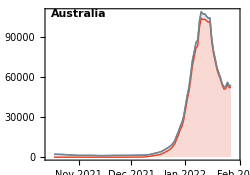
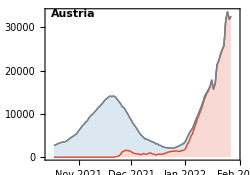
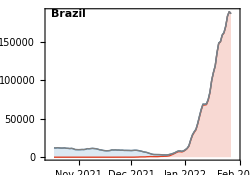
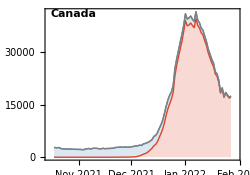
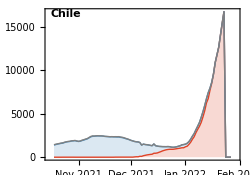
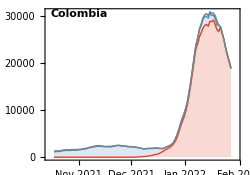
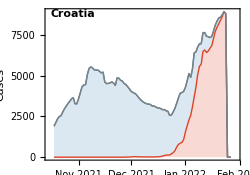
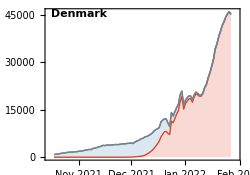
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=500000;
```

```mathematica
splitCaseLogPlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{50,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[country_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{50,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[country_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[country,"Omicron"];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->200,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{50,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[3]],FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.88,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
legendsForCountries=Map[constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather[#,"Omicron"]],"Omicron",legendStartingPointY- 0.09,colors[[3]]]&,countries];
```

```mathematica
panels=MapThread[Show[splitCaseLogPlot[#1,#2],splitCaseLogPlotModeledOmicron[#1]]&,{countries,legendsForCountries}];
```

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_partitioned-log-cases.png